```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/yunqiguo/Document/CS249_2/project/249-Sun/src

```mathematica
<<../data/edges.mx
```

```mathematica
g=Graph[edges];
```

```mathematica
subG=Subgraph[g,RandomSample[VertexList[g][[1;;500]]]];
```

```mathematica
subG=Subgraph[subG,RandomSample@ConnectedComponents[subG][[1]]];
```

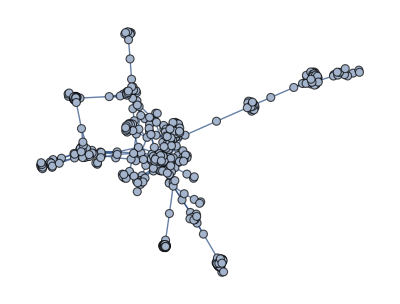

```mathematica
Graph[subG,VertexSize->30]
```

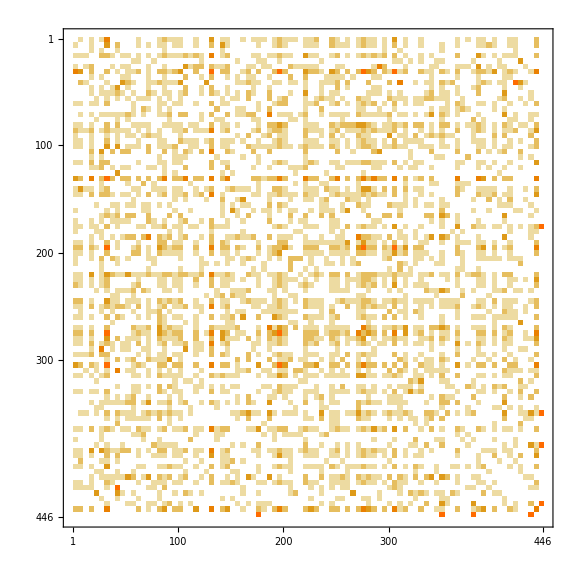

```mathematica
(adjMatrix=AdjacencyMatrix[subG])//MatrixPlot
```

```mathematica
communities1=FindGraphPartition[subG,15];
```

```mathematica
Length@Flatten@communities1
```

446

```mathematica
newOrder=Flatten[Position[VertexList[subG],#]&/@Flatten[communities1]];
```

```mathematica
CommunityGraphPlot[subG,communities1]
```

-Graphics-

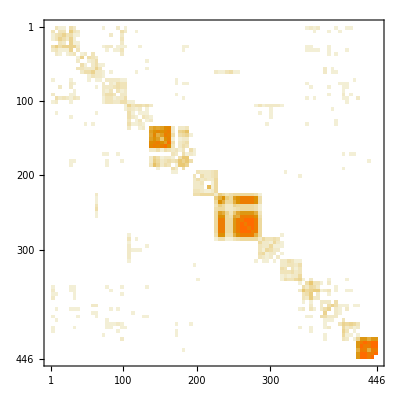

```mathematica
(adjMatrix[[newOrder,newOrder]])//MatrixPlot
```

```mathematica
distance=GraphDistanceMatrix[subG];
vDic = Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[subG];
```

```mathematica
communities=FindGraphPartition[subG,15];
Length@communities
communityDistanceMatrix=Table[N@Mean@Flatten@distance[[vDic/@communities[[i]],vDic/@communities[[j]]]],{i,Length@communities},{j,Length@communities}];
g2=WeightedAdjacencyGraph[1/communityDistanceMatrix];
(*Export["communityDistanceMatrix.csv",communityDistanceMatrix//TableForm];*)
communities4=FindGraphPartition[g2,6];
Length@communities4
c4Size=Length@communities4;
distance2=GraphDistanceMatrix[g2];
vDic2= Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g2];
communityDistanceMatrix2=Table[N@Mean@Flatten@distance2[[vDic2/@communities4[[i]],vDic2/@communities4[[j]]]],{i,c4Size},{j,c4Size}];
nearests=Position[#,Min[#]][[1,1]]&/@ communityDistanceMatrix2[[6;;,1;;5]];
communities5=Table[
Join[communities4[[i]],Flatten@ communities4[[ Position[nearests,i][[All,1]] +5]]],{i,5}];
```

15

6

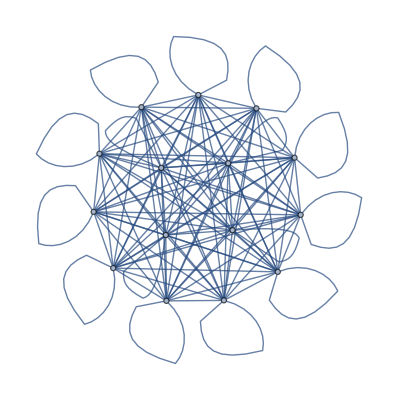

```mathematica
g2
```

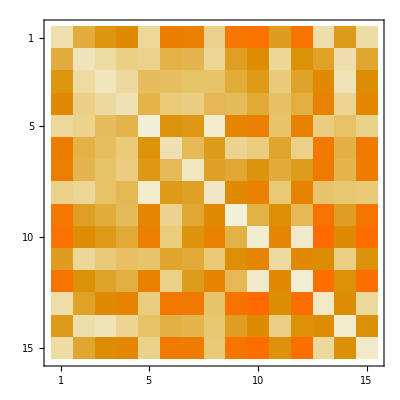

```mathematica
communityDistanceMatrix//MatrixPlot
```

```mathematica
CommunityGraphPlot[g2,FindGraphPartition[g2,3],VertexSize->Large]
```

-Graphics-

```mathematica
CommunityGraphPlot[subG,FindGraphPartition[subG,3]]
```

-Graphics-